```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadAddOns={"FeynArts"};
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
(*Why is this?*)
$KeepLogDivergentScalelessIntegrals=True;
```

## Get Feynman diagrams

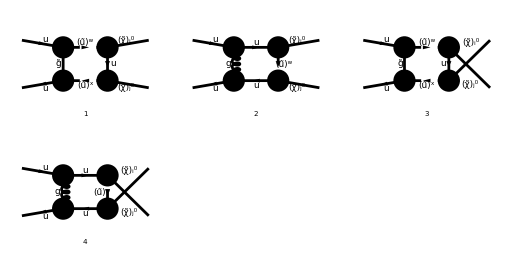

```mathematica
BoxDiagrams = InsertFields[CreateTopologies[1, 2->2,ExcludeTopologies->{Triangles,SelfEnergies,Tadpoles}], {F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling},ExcludeParticles->{V[1],V[2],V[3],F[11],F[12],S[1],S[2],S[3],S[4]}];
Paint[BoxDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

## Convert diagrams to amplitudes

```mathematica
(*Box-loop diagrams*)
Subscript[M, box][0]=FCFAConvert[CreateFeynAmp[BoxDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},LoopMomenta->{qloop},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]//.AmpSimplifyRules;
```

```mathematica
(*Replacing couplings*)
Subscript[M, box][1]=Subscript[M, box][0]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.QSimplifyRules//Simplify;
```

```mathematica
Subscript[M, box][2]=TraceLoopAmp/@Subscript[M, box][1];
```

```mathematica
(*Subscript[M, box][3]=EvalPVLoopAmp/@Subscript[M, box][2];
CheckPVRemainder/@Subscript[M, box][3]*)
```

```mathematica
Prefactor=8 π^2 SMP["g_s"]^2 SMP["g_W"]^2 CF SUNFDelta[SUNFIndex[a],SUNFIndex[b]]
```

```mathematica
temp[0]=(TID[DiracSimplify[Contract[#1/Prefactor]],qloop,ToPaVe->True]&)[Part[Subscript[M, box][2],2]];
```

```mathematica
temp[1]=FeynAmpDenominatorExplicit[(#1/. (h:PaVe)[x__]:>TrickMandelstam[h[x],MandelstamParameters]&)[temp[0]]];
```

```mathematica
temp[2]=(Collect2[#1,PaVe,Factoring->Function[x,Factor2[TrickMandelstam[x,MandelstamParameters]]]]&)[temp[1]]
```

```mathematica
Itemp[0]=SquareAmplitudes[temp[2],Subscript[M̄, s][0]]
```

```mathematica
Subscript[M, box][4]=(SelectNotFree2[#1,{A0,B0,C0,D0}]&)/@Select[Subscript[M, box][3],CheckPVRemainder]
```

```mathematica
Subscript[I, sbox][0]=(SquareAmplitudes[#1,Subscript[M̄, s][0]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.SuperChargeRules//FullSimplify&)/@(ReplaceAll[#1,{Index[Sfermion,5]->A,Index[Sfermion,6]->C}]&)/@Subscript[M, box][4]
Subscript[I, tbox][0]=(SquareAmplitudes[#1,ReplaceAll[Subscript[M̄, t][0],A->C]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.SuperChargeRules//FullSimplify&)/@(ReplaceAll[#1,{Index[Sfermion,5]->A,Index[Sfermion,6]->C}]&)/@Subscript[M, box][4]
Subscript[I, ubox][0]=(SquareAmplitudes[#1,ReplaceAll[Subscript[M̄, u][0],A->C]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.SuperChargeRules//FullSimplify&)/@(ReplaceAll[#1,{Index[Sfermion,5]->A,Index[Sfermion,6]->C}]&)/@Subscript[M, box][4]
```

```mathematica
ReduceMandelstam[Subscript[I, sbox][0]]
```

```mathematica
(Collect2[SelectFree2[ChangeDimension[#1,4]//DiracSimplify,FeynCalc`Eps],D0]//FeynAmpDenominatorExplicit//DiracSimplify&)/@ReplaceAll[Subscript[I, sbox][0],D->4]
```

```mathematica
Collect2[%,D0]
```

```mathematica
(*Replacement rules for limit of D->4 of Passarino-Veltman functions*)
PaVeEvalRules={D0[args__,m1_,m2_,m3_,m4_]:>LoopRefine[PVD[0,0,0,0,args,m1^(1/2),m2^(1/2),m3^(1/2),m4^(1/2)]]};
```

```mathematica
Subscript[I, sbox][1]=PaVeOrder[Subscript[I, sbox][0]]//.PaVeEvalRules;
```

```mathematica
Collect2[SelectFree2[ChangeDimension[ReplaceAll[Subscript[I, sbox][0],D->4],4]//DiracSimplify,FeynCalc`Eps]//Simplify,D0]
```